CreateDirectory::filex: /home/dvl/Desktop/ucr/2017-iii/431/latex/trabajo/tarea3/mathematica-img already exists.

$Failed

/home/dvl/Desktop/ucr/2017-iii/431/latex/trabajo/tarea3/mathematica-img

/home/dvl/Desktop/ucr/2017-iii/431/latex/trabajo/tarea3/mathematica-img

Set

1/(s (3+s) (5+s))

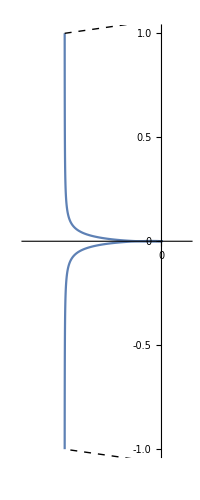

a1.eps

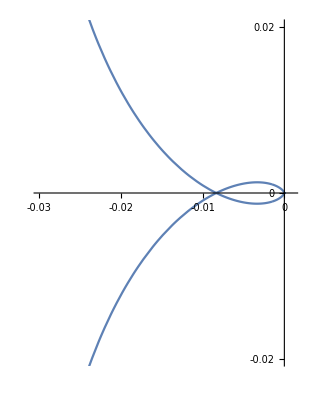

a2.eps

B

(-3+s)/(1+s)^2

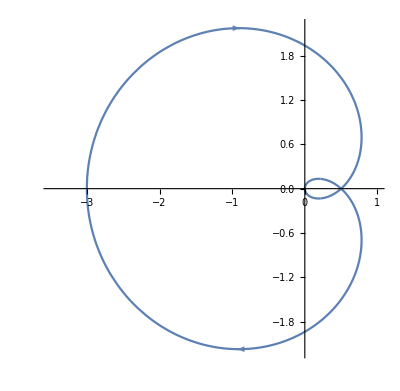

```mathematica
CreateDirectory["mathematica-img"]
SetDirectory["mathematica-img"]
Directory[]

Set
tfe=1/(s(s+3)(s+5))

na1=NyquistPlot[tfe,PlotRange->{{-0.05,0.01},{-1,1}},PlotRangePadding->Automatic]
Export["a1.eps",na1]

na2=NyquistPlot[tfe,PlotRange->{{-0.03,0.001},{-0.02,0.02}},PlotRangePadding->Automatic]
Export["a2.eps",na2]

B
tfe=(s-3)/(s+1)^2

nb1=NyquistPlot[tfe,PlotRange->{{-3.5,1},{-2.2,2.2}},PlotRangePadding->Automatic]
Export["b1.eps",nb1]

C
tfe=((s+4)(s+7))/((s-3)(s-5))

nc1=NyquistPlot[tfe,PlotRange->2,PlotRangePadding->Automatic]
Export["c1.eps",nc1]

D
tfe=((s+1)(s+2))/(s(s+4)(s-1))

nd1=NyquistPlot[tfe,PlotRange->{{-2,0.1},{-10,10}},PlotRangePadding->Automatic]
Export["d1.eps",nd1]

nd2=NyquistPlot[tfe,PlotRange->{{-1,0.01},{-1,1}},PlotRangePadding->Automatic]
Export["d2.eps",nd2]

E
T4=100;
T1=1;
T2=5;
T3=10;

tfe=(10*(T4 s+1))/(s* (T3 s+1)* (T2 s+1)* (T1 s+1))

ne1=NyquistPlot[tfe,PlotRange->{{-250,1250},{-2500,2500}},PlotRangePadding->Automatic]
Export["e1.eps",ne1]

ne2=NyquistPlot[tfe,PlotRange->{{-150,0.01},{-100,100}},PlotRangePadding->Automatic]
Export["e2.eps",ne2]

F
tfe=((4 s+1) (2 s+1))/(s^2 (s-1))

npf1=NyquistPlot[tfe,PlotRange->{{-10,0.01},{-20,20}},PlotRangePadding->Automatic]
Export["f1.eps",npf1]

npf2=NyquistPlot[tfe,PlotRange->{{-10,1000},{-250,250}},PlotRangePadding->Automatic]
Export["f2.eps",npf2]

G
tfe=((0.1 s+1) (1 s+1))/s^3

npg1=NyquistPlot[tfe,PlotRange->{{-200,0.01},{-2000,2000}},PlotRangePadding->Automatic]
Export["g1.eps",npg1]

npg2=NyquistPlot[tfe,PlotRange->{{-0.2,0.01},{-0.1,0.1}},PlotRangePadding->Automatic]
Export["g2.eps",npg2]
```